## Numerical results for trophical transmission model with multiple infections

```mathematica
SetDirectory[NotebookDirectory[]]
ParallelNeeds["Tools`"](* Import package Tools that define useful functions*)
```

/Users/phuongnguyen/Work/multipleinfections/code

# ODEs

```mathematica
dIsdt = R[Iw, Is, Iww]- d Is- Πs[Ds, Dw, Dww] Is  - ηw  Is ;
dIwdt =  (1-p)ηw Is  - (d + αw)Iw - Πw[Ds, Dw,Dww, βw]Iw; 
dIwwdt =  p ηw Is  - (d + αww)Iww - Πww[Ds, Dw, Dww,βww]Iww; 
dDsdt =B[Ds, Dw,Dww, Is, Iw, Iww]  - μ Ds - (λww + λw) Ds;
dDwdt =(λw + 2(1-q)λww) Ds- (μ + σw) Dw - (2(1-q)λww +λw)Dw;
dDwwdt = q λww Ds + (2(1-q)λww + λw)Dw - (μ + σww)Dww;
dWdt = fw Dw +fww Dww- δ W - ηw Is;

forceInf = {ηw -> γ W, λw -> βw Iw, λww -> βww Iww};
odesRes = {dIsdt, dIwdt, dIwwdt, dDsdt, dDwdt, dDwwdt, dWdt};
varRes = {Is, Iw, Iww, Ds, Dw, Dww, W};
vartRes = {Is[t], Iw[t], Iww[t], Ds[t], Dw[t], Dww[t], W[t]};
```

# Graph format and parallel computation

```mathematica
includeFrame = True;
imageSize = Medium;
frameStyle = Directive[Black,Thickness[0.003]];
colorlist = ColorData[97,"ColorList"]
DistributeDefinitions[NSolveCodim2Positive];
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

# Linear birth function for intermediate host

```mathematica
func0 = {R[Iw, Is, Iww] -> r(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]->  βw(Ds + Dw+Dww),Πww[Ds, Dw,Dww, βww]->  βww(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};
sysfunc0 = odesRes/.forceInf/.func0;
sysNDSolvefunc0 = MakeSystem[varRes, t,sysfunc0];
```

## Jacobian matrix

```mathematica
Jmatfunc0 = D[sysfunc0, {varRes}];
```

## Ecological trajectories

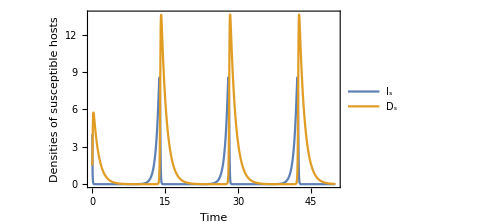
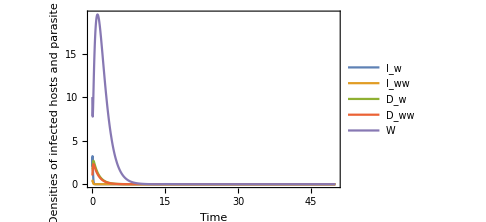
-Graphics- | -Graphics-

```mathematica
prEco0 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 0.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 6.5,fww-> 7.5, δ-> 0.9};

maxt = 50;

init0= {Is[0]== 4, Iw[0] == 2,Iww[0]==0.3, Ds[0] ==1.5, Dw[0] == 1.7,Dww[0]==1, W[0] == 10};

sols0 = NSolve[Thread[(odesRes/.func0/.forceInf/.prEco0) == 0], varRes];
ndsol0 = NDSolve[Join[sysNDSolvefunc0/.prEco0, init0], varRes, {t, 0, maxt}] ;

p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, maxt}, All}, PlotLegends->{"I_s",  "D_s"}, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->imageSize,Frame->includeFrame,FrameStyle->frameStyle];

p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, maxt}, All},PlotLegends->{"I_w", "I_ww", "D_w", "D_ww", "W"}, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->imageSize, Frame-> includeFrame];
Grid[{{p1, p2}}]
(*Export["diseasefree_linear.jpg",%]*)
```

## Bifurcation γ

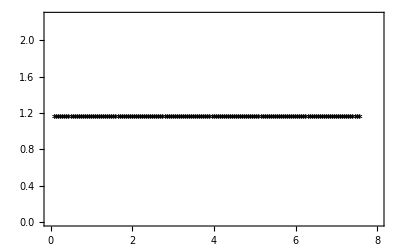

```mathematica
parγ = {ρ -> 1.2, d -> 0.1,r -> 2.5, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 1.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 1.1};
γrange = Range[0.1, 8, 0.05];

solsγ = NSolve[Thread[(odesRes/.func0/.forceInf/.parγ/.γ-> 0.1) == 0], varRes];
eqinit = {Is->1.1309523809523814,Iw->0,Iww->0,Ds->2.0000000000000004,Dw->0,Dww->0,W->0};

eqγzero = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, eqinit];
{#}& /@Transpose[{γrange, Is/.eqγzero}];
p0 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc0, parγ, γ, γrange, eqγzero], PlotStyle-> Black, Frame->includeFrame, FrameLabel->{"Pool to intermediate host transmission (γ)", "Equilibrium"}, PlotLegends->{"I_s"}];
{#}& /@Transpose[{γrange, Ds/.eqγzero}];
p1 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc0, parγ, γ, γrange, eqγzero], PlotStyle-> Gray, PlotLegends->{"D_s"}];
Show[p0, p1]
```

## Bifurcation β_w

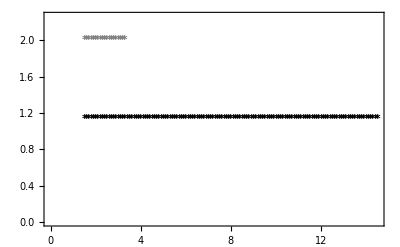

```mathematica
parβw = {ρ -> 1.2, d -> 0.1,r -> 2.5, γ -> 3.5, αw-> 0, αww-> 0,  βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 1.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 1.1, Κ-> 100};
βwrange = Range[1.5, 14.5, 0.1];

solsβw = NSolve[Thread[(sysfunc0/.parβw/.βw-> 1.5) == 0], varRes];

eqinit = {Is->1.1309523809523812,Iw->0,Iww->0,Ds->2.0000000000000004,Dw->0,Dww->0,W->0};

eqβwzero = FollowRoot[sysfunc0, parβw, βw, βwrange, varRes, eqinit];
{#}& /@Transpose[{βwrange, Is/.eqβwzero}];
p0 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc0, parβw, βw, βwrange, eqβwzero], PlotStyle-> Black, Frame->includeFrame, FrameLabel->{"Intermediate - definitive hosts transmission β_w", "Equilibrium"}, PlotLegends->{"I_s"}];
{#}& /@Transpose[{βwrange, Ds/.eqβwzero}];
p1 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc0, parβw, βw, βwrange, eqβwzero], PlotStyle-> Gray, PlotLegends->{"D_s"}];
Show[p0, p1]
```

# Nonlinear birth function for intermediate host

```mathematica
func1 = {R[Iw, Is, Iww] -> r(1-k(Is + Iw+Iww))(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]->  βw(Ds + Dw+ Dww),Πww[Ds, Dw, Dww, βww]->  βww(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};

sysfunc1 = odesRes/.forceInf/.func1;
sysNDSolvefunc1 = MakeSystem[varRes, t, sysfunc1];
```

## Jacobian matrix

```mathematica
Jmatfunc1 = D[sysfunc1, {varRes}];
```

## Ecological trajectories

## Disease free equilibrium

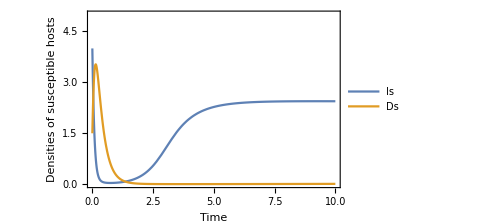
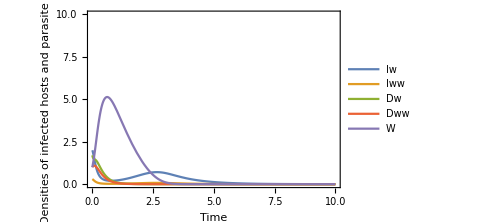
-Graphics- | -Graphics-

```mathematica
prEcoNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 0.9, k -> 0.26};

maxt = 10;

solsNL = NSolve[Thread[(sysfunc1/.prEcoNL) == 0], varRes];

{Is[0]== 4, Iw[0] == 2,Iww[0]==0.3, Ds[0] ==1.5, Dw[0] == 1.7,Dww[0]==1, W[0] == 1};
ndsolNL = NDSolve[Join[sysNDSolvefunc1/.prEcoNL, %], varRes, {t, 0, maxt}] ;

p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsolNL], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 5}}, PlotLegends->{"Is",  "Ds"},Frame->includeFrame,FrameStyle->frameStyle, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->imageSize];

p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsolNL], {t, 0, maxt}, PlotRange->{{0, maxt},{0, 10}},PlotLegends->{"Iw", "Iww", "Dw", "Dww", "W"}, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->imageSize];
Grid[{{p1, p2}}]
(*Export["Diseasefree.jpeg",%]*)
```

## Disease stable equilibrium

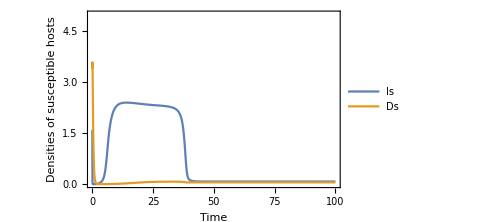
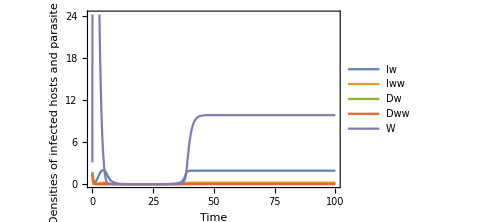
-Graphics- | -Graphics-

```mathematica
prEcoDSNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, α-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σ-> 0,q-> 0.01, fw -> 49, fww-> 49*8.51,δ-> 0.9, k -> 0.26};

condsimplifyNL = {αw-> α, αww-> α, σw-> σ, σww-> σ};

maxt = 100;

{Is[0]== 1.6, Iw[0] == 1.2,Iww[0]==0.32, Ds[0] ==3.4, Dw[0] == 1.7,Dww[0]==1.1, W[0] == 3.1};
ndsolDS = NDSolve[Join[sysNDSolvefunc1/.condsimplifyNL/.prEcoDSNL, %], varRes, {t, 0, maxt}, AccuracyGoal->Infinity] ;

solsDS = NSolve[Thread[(sysfunc1/.condsimplifyNL/.prEcoDSNL) == 0], varRes];

p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsolDS], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 5}}, PlotLegends->{"Is",  "Ds"},Frame-> includeFrame, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->imageSize];
p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsolDS], {t, 0, maxt}, PlotRange->{{0, maxt},{0, 24.2}},PlotLegends->{"Iw", "Iww", "Dw", "Dww", "W"}, Frame-> includeFrame, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->imageSize];
Grid[{{p1, p2}}]
```

## Bifurcation f_w (f_ww = ϵ f_w)

CALCULATION

```mathematica
parfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 1};
fwrangeFWrd = Range[40.5, 51.5, 0.05];
fwrangeBWrd = Range[40.5, 32, -0.05];
fwrange = Range[32, 51.5, 0.3];

(*Find all solutions of the system with the given parameter values*)
solsfwAll = NSolve[Thread[(odesRes/.func1/.forceInf/.fww-> ϵ fw/.parfw/.fw-> 40.5) == 0], varRes, Reals];

(*Select disease circulation solutions*)
solsfw= Select[solsfwAll, (Is/.#)> 0 &&(Iw/.#)> 0 &&(Iww/.#)> 0 &&(W/.#)> 0 &][[1]];

(*Select disease free solutions*)
solsfwzero = Select[solsfwAll, (Is/.#)> 0 &&(Iw/.#)== 0 &&(Iww/.#)== 0&&(Ds/.#)>0 &&(Dw/.#)== 0 &&(Dww/.#)== 0 &&(W/.#)== 0 &][[1]];

eqfwFWrd = FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, fwrangeFWrd, varRes, solsfw];
eqfwBWrd = FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, fwrangeBWrd, varRes, solsfw];

rangeIs = {{fwrangeBWrd[[-1]], fwrangeFWrd[[-1]]}, {-0.1, 2}};
rangeDs = {{fwrangeBWrd[[-1]], fwrangeFWrd[[-1]]}, {-0.01, 0.03}};
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::reged: The point {2.32041,0.000842335,0.0000935928,0.0759001,0.0000300178,0.,0.000140786} is at the edge of the search region {0.,∞} in coordinate 6 and the computed search direction points outside the region.

PLOTTING

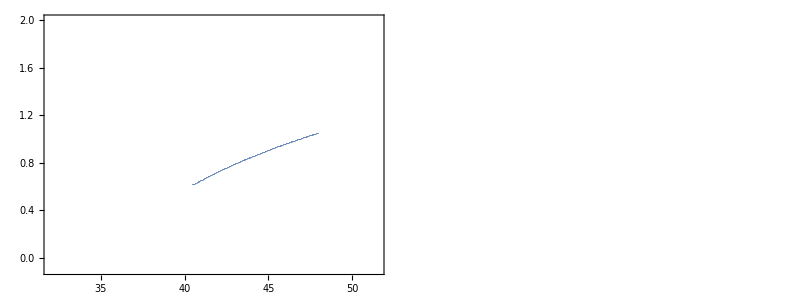

```mathematica
xaxis =fwrangeFWrd[[1;; Length[eqfwFWrd]]];
 {#}& /@Transpose[{xaxis, Iw/.eqfwFWrd}];
p0 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, xaxis, eqfwFWrd], PlotStyle->colorlist[[1]], PlotRange->rangeIs, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Parasite reproduction in single infection(f_w)", "Equilibrium I_w"}];

{#}& /@Transpose[{xaxis, Dw/.eqfwFWrd}];
p1 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, xaxis, eqfwFWrd], PlotStyle-> colorlist[[2]], PlotRange->rangeDs, ImageSize->imageSize, Frame->includeFrame, FrameLabel->{"Parasite reproduction in single infection(f_w)", "Equilibrium D_w"}];

xaxis = fwrangeBWrd[[1;;Length[eqfwBWrd]]];
{#}& /@Transpose[{xaxis, Iw/.eqfwBWrd}];
p2 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, xaxis, eqfwBWrd], PlotStyle->colorlist[[1]], PlotRange->rangeIs, ImageSize->imageSize];

{#}& /@Transpose[{xaxis, Dw/.eqfwBWrd}];
p3 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, xaxis, eqfwBWrd], PlotStyle->colorlist[[2]], PlotRange->rangeDs, ImageSize->imageSize];


eqfwzero = ConstantArray[solsfwzero, Length[fwrange]];
{#}& /@Transpose[{fwrange, Iw/.eqfwzero}];
p4 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero], PlotStyle->colorlist[[1]], PlotRange->rangeIs, ImageSize->imageSize];

{#}& /@Transpose[{fwrange, Dw/.eqfwzero}];
p5 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero], PlotStyle->colorlist[[2]], PlotRange->rangeDs, ImageSize->imageSize];

pp0 = Show[p0,  p2, p4];
pp1 = Show[p1, p3, p5];

Grid[{{pp0, pp1}}]
(*Export["bifurcation_fw_NL.jpg", %]*)
```

```mathematica
On[Assert];
rr= Range[35, 37, 0.02];
FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, rr, varRes, solsfwzero];
xx =ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, rr, %];
pos = Position[xx, "*", 1, 1][[1]][[1]];
xx[[pos]] == "*"//Assert
xx[[pos-1]] == "." //Assert
fwbifur = rr[[pos]]
```

35.84

## Bifurcation ϵ and f_w (f_ww = ϵ f_w)

CALCULATION

```mathematica
parϵfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26};

ϵstart = 0.1;
ϵend = 4;
ϵinterval = 0.5;
fwstart = 32;
fwend = 40;
fwinterval = 2;

ϵfwAllresults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parϵfw, {ϵ -> i}, {fw-> j}, ϵfw, eq,varRes],{i, ϵstart, ϵend, ϵinterval}, {j, fwstart, fwend, fwinterval}];
```

{{0.1,32},{}}

{{0.6,32},{}}

{{1.1,32},{}}

{{1.6,32},{}}

{{3.6,32},{{Is→2.19244,Iw→0.107081,Iww→0.0118979,Ds→0.0764393,Dw→0.00365701,Dww→0.000187248,W→0.0190954},{Is→0.508013,Iw→1.55271,Iww→0.172523,Ds→0.0599363,Dw→0.0252625,Dww→0.0184455,W→1.236}}}

{{2.6,32},{{Is→2.07792,Iw→0.202795,Iww→0.0225327,Ds→0.0764179,Dw→0.00663989,Dww→0.000638458,W→0.038348},{Is→0.96971,Iw→1.15052,Iww→0.127836,Ds→0.065723,Dw→0.0230419,Dww→0.0124717,W→0.478156}}}

{{2.1,32},{}}

{{3.1,32},{{Is→2.15395,Iw→0.13918,Iww→0.0154645,Ds→0.0764792,Dw→0.00468848,Dww→0.000310743,W→0.0253072},{Is→0.673988,Iw→1.40779,Iww→0.156421,Ds→0.0619947,Dw→0.0246615,Dww→0.0163281,W→0.843881}}}

{{0.1,34},{}}

{{0.6,34},{}}

{{1.1,34},{}}

{{1.6,34},{}}

{{3.6,34},{{Is→2.26782,Iw→0.0444061,Iww→0.00493401,Ds→0.0762036,Dw→0.00155542,Dww→0.000033856,W→0.00762751},{Is→0.43928,Iw→1.61282,Iww→0.179202,Ds→0.0590964,Dw→0.0254574,Dww→0.0193065,W→1.48518}}}

{{2.1,34},{{Is→2.16943,Iw→0.126266,Iww→0.0140295,Ds→0.0764692,Dw→0.00427722,Dww→0.000257542,W→0.0227793},{Is→1.19577,Iw→0.954823,Iww→0.106091,Ds→0.0685513,Dw→0.0212103,Dww→0.00953087,W→0.320911}}}

{{2.6,34},{{Is→2.22779,Iw→0.0776547,Iww→0.00862831,Ds→0.0763562,Dw→0.00268445,Dww→0.00010035,W→0.0136052},{Is→0.790296,Iw→1.30645,Iww→0.145161,Ds→0.063456,Dw→0.0241163,Dww→0.0148194,W→0.66732}}}

{{0.1,36},{{Is→2.31062,Iw→0.00894157,Iww→0.000993508,Ds→0.0759659,Dw→0.000317395,Dww→1.62196×10^-6,W→0.00150406}}}

{{3.1,34},{{Is→2.25323,Iw→0.0565146,Iww→0.0062794,Ds→0.0762667,Dw→0.00197022,Dww→0.000054089,W→0.00977737},{Is→0.569946,Iw→1.49859,Iww→0.16651,Ds→0.0606998,Dw→0.0250608,Dww→0.0176612,W→1.06296}}}

{{0.6,36},{{Is→2.29619,Iw→0.02089,Iww→0.00232111,Ds→0.0760551,Dw→0.000738273,Dww→7.9157×10^-6,W→0.0035387}}}

{{1.1,36},{{Is→2.13499,Iw→0.155026,Iww→0.0172251,Ds→0.0764806,Dw→0.00518615,Dww→0.000382322,W→0.0284626}}}

{{0.1,38},{{Is→2.17379,Iw→0.122624,Iww→0.0136249,Ds→0.076465,Dw→0.00416033,Dww→0.000243388,W→0.0220735}}}

{{1.6,36},{{Is→1.49864,Iw→0.694237,Iww→0.0771375,Ds→0.0721097,Dw→0.0177184,Dww→0.00579329,W→0.185198}}}

{{3.6,36},{{Is→0.386882,Iw→1.65868,Iww→0.184298,Ds→0.0584617,Dw→0.0255867,Dww→0.0199556,W→1.73464}}}

{{2.6,36},{{Is→0.668401,Iw→1.41266,Iww→0.156962,Ds→0.0619248,Dw→0.0246849,Dww→0.0164001,W→0.853911}}}

{{2.1,36},{{Is→0.974392,Iw→1.14646,Iww→0.127385,Ds→0.0657822,Dw→0.0230097,Dww→0.0124104,W→0.474155}}}

{{3.1,36},{{Is→0.493721,Iw→1.5652,Iww→0.173911,Ds→0.059761,Dw→0.0253055,Dww→0.0186253,W→1.2821}}}

{{0.6,38},{{Is→2.05998,Iw→0.21784,Iww→0.0242044,Ds→0.0763788,Dw→0.00708319,Dww→0.000731134,W→0.0415819}}}

{{1.1,38},{{Is→1.75373,Iw→0.476513,Iww→0.0529459,Ds→0.0746148,Dw→0.0136348,Dww→0.00306386,W→0.107954}}}

{{0.1,40},{{Is→2.05673,Iw→0.22056,Iww→0.0245067,Ds→0.0763707,Dw→0.00716261,Dww→0.000748484,W→0.0421731},{Is→2.05673,Iw→0.22056,Iww→0.0245067,Ds→0.0763707,Dw→0.00716261,Dww→0.000748484,W→0.0421731}}}

{{1.6,38},{{Is→1.24037,Iw→0.916329,Iww→0.101814,Ds→0.069098,Dw→0.0207767,Dww→0.0089604,W→0.296706}}}

{{0.6,40},{{Is→1.88505,Iw→0.365188,Iww→0.0405764,Ds→0.0755902,Dw→0.0110581,Dww→0.00190668,W→0.0766626}}}

{{3.6,38},{{Is→0.345582,Iw→1.69485,Iww→0.188316,Ds→0.0579651,Dw→0.0256775,Dww→0.0204627,W→1.98458}}}

{{2.6,38},{{Is→0.578769,Iw→1.49088,Iww→0.165654,Ds→0.0608091,Dw→0.0250299,Dww→0.0175489,W→1.04132}}}

{{2.1,38},{{Is→0.824573,Iw→1.27662,Iww→0.141847,Ds→0.0638886,Dw→0.023934,Dww→0.0143721,W→0.624802}}}

{{1.1,40},{{Is→1.52997,Iw→0.667396,Iww→0.0741551,Ds→0.0724494,Dw→0.0172777,Dww→0.0054314,W→0.174275}}}

{{3.1,38},{{Is→0.435307,Iw→1.61629,Iww→0.179588,Ds→0.0590481,Dw→0.0254678,Dww→0.0193559,W→1.502}}}

{{1.6,40},{{Is→1.06124,Iw→1.07118,Iww→0.11902,Ds→0.0668761,Dw→0.0223701,Dww→0.0112745,W→0.406369}}}

{{2.6,40},{{Is→0.509874,Iw→1.55108,Iww→0.172342,Ds→0.0599592,Dw→0.0252568,Dww→0.018422,W→1.23019}}}

{{2.1,40},{{Is→0.713599,Iw→1.37325,Iww→0.152584,Ds→0.062491,Dw→0.0244881,Dww→0.0158161,W→0.777278}}}

{{3.1,40},{{Is→0.389094,Iw→1.65674,Iww→0.184082,Ds→0.0584884,Dw→0.0255816,Dww→0.0199284,W→1.72275}}}

{{3.6,40},{{Is→0.312191,Iw→1.7241,Iww→0.191567,Ds→0.0575661,Dw→0.0257441,Dww→0.0208695,W→2.235}}}

```mathematica
ϵfwAllresults
```

{{{},{},{ϵfw→{0.1,36},eq→{Is→2.31062,Iw→0.00894157,Iww→0.000993508,Ds→0.0759659,Dw→0.000317395,Dww→1.62196×10^-6,W→0.00150406}},{ϵfw→{0.1,38},eq→{Is→2.17379,Iw→0.122624,Iww→0.0136249,Ds→0.076465,Dw→0.00416033,Dww→0.000243388,W→0.0220735}},Null},{{},{},{ϵfw→{0.6,36},eq→{Is→2.29619,Iw→0.02089,Iww→0.00232111,Ds→0.0760551,Dw→0.000738273,Dww→7.9157×10^-6,W→0.0035387}},{ϵfw→{0.6,38},eq→{Is→2.05998,Iw→0.21784,Iww→0.0242044,Ds→0.0763788,Dw→0.00708319,Dww→0.000731134,W→0.0415819}},{ϵfw→{0.6,40},eq→{Is→1.88505,Iw→0.365188,Iww→0.0405764,Ds→0.0755902,Dw→0.0110581,Dww→0.00190668,W→0.0766626}}},{{},{},{ϵfw→{1.1,36},eq→{Is→2.13499,Iw→0.155026,Iww→0.0172251,Ds→0.0764806,Dw→0.00518615,Dww→0.000382322,W→0.0284626}},{ϵfw→{1.1,38},eq→{Is→1.75373,Iw→0.476513,Iww→0.0529459,Ds→0.0746148,Dw→0.0136348,Dww→0.00306386,W→0.107954}},{ϵfw→{1.1,40},eq→{Is→1.52997,Iw→0.667396,Iww→0.0741551,Ds→0.0724494,Dw→0.0172777,Dww→0.0054314,W→0.174275}}},{{},{},{ϵfw→{1.6,36},eq→{Is→1.49864,Iw→0.694237,Iww→0.0771375,Ds→0.0721097,Dw→0.0177184,Dww→0.00579329,W→0.185198}},{ϵfw→{1.6,38},eq→{Is→1.24037,Iw→0.916329,Iww→0.101814,Ds→0.069098,Dw→0.0207767,Dww→0.0089604,W→0.296706}},{ϵfw→{1.6,40},eq→{Is→1.06124,Iw→1.07118,Iww→0.11902,Ds→0.0668761,Dw→0.0223701,Dww→0.0112745,W→0.406369}}},{{},Null,{ϵfw→{2.1,36},eq→{Is→0.974392,Iw→1.14646,Iww→0.127385,Ds→0.0657822,Dw→0.0230097,Dww→0.0124104,W→0.474155}},{ϵfw→{2.1,38},eq→{Is→0.824573,Iw→1.27662,Iww→0.141847,Ds→0.0638886,Dw→0.023934,Dww→0.0143721,W→0.624802}},{ϵfw→{2.1,40},eq→{Is→0.713599,Iw→1.37325,Iww→0.152584,Ds→0.062491,Dw→0.0244881,Dww→0.0158161,W→0.777278}}},{Null,Null,{ϵfw→{2.6,36},eq→{Is→0.668401,Iw→1.41266,Iww→0.156962,Ds→0.0619248,Dw→0.0246849,Dww→0.0164001,W→0.853911}},{ϵfw→{2.6,38},eq→{Is→0.578769,Iw→1.49088,Iww→0.165654,Ds→0.0608091,Dw→0.0250299,Dww→0.0175489,W→1.04132}},{ϵfw→{2.6,40},eq→{Is→0.509874,Iw→1.55108,Iww→0.172342,Ds→0.0599592,Dw→0.0252568,Dww→0.018422,W→1.23019}}},{Null,Null,{ϵfw→{3.1,36},eq→{Is→0.493721,Iw→1.5652,Iww→0.173911,Ds→0.059761,Dw→0.0253055,Dww→0.0186253,W→1.2821}},{ϵfw→{3.1,38},eq→{Is→0.435307,Iw→1.61629,Iww→0.179588,Ds→0.0590481,Dw→0.0254678,Dww→0.0193559,W→1.502}},{ϵfw→{3.1,40},eq→{Is→0.389094,Iw→1.65674,Iww→0.184082,Ds→0.0584884,Dw→0.0255816,Dww→0.0199284,W→1.72275}}},{Null,Null,{ϵfw→{3.6,36},eq→{Is→0.386882,Iw→1.65868,Iww→0.184298,Ds→0.0584617,Dw→0.0255867,Dww→0.0199556,W→1.73464}},{ϵfw→{3.6,38},eq→{Is→0.345582,Iw→1.69485,Iww→0.188316,Ds→0.0579651,Dw→0.0256775,Dww→0.0204627,W→1.98458}},{ϵfw→{3.6,40},eq→{Is→0.312191,Iw→1.7241,Iww→0.191567,Ds→0.0575661,Dw→0.0257441,Dww→0.0208695,W→2.235}}}}

```mathematica
NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parϵfw, {ϵ -> 3.6}, {fw-> 32}, ϵfw, eq,varRes]
```

{{3.6,32},{{Is→2.19244,Iw→0.107081,Iww→0.0118979,Ds→0.0764393,Dw→0.00365701,Dww→0.000187248,W→0.0190954},{Is→0.508013,Iw→1.55271,Iww→0.172523,Ds→0.0599363,Dw→0.0252625,Dww→0.0184455,W→1.236}}}

```mathematica
ParallelTa
```

PLOT

```mathematica
eqϵfw =eq/. Flatten[ϵfwAllresults, 1];
ϵfwlist = ϵfw/.Flatten[ϵfwAllresults, 1];

rangeϵfw= {{ϵstart, ϵend}, {fwstart, fwend}};
imsize = 300;
marklist = ListStableMarkCodim2[Jmatfunc1/.fww-> ϵ fw, parϵfw,{ϵ, fw}, ϵfwlist,eqϵfw, True];
p0 = ListPlot[ϵfwlist,  PlotStyle->marklist, PlotRange->rangeϵfw, ImageSize->imsize, Frame-> {{True, False}, {True,False}}, FrameLabel->{"ϵ", "Reproduction in single infection f_w"}, GridLines->{{1},{}}, GridLinesStyle-> {Thick,Black}]
(*Export["bifurcation_epsilonfw_NL.jpg", %]*)
```

ReplaceAll::rmix: Elements of {{},{},{ϵfw→{0.1,36},eq→{Is→2.31062,Iw→0.00894157,Iww→0.000993508,Ds→0.0759659,Dw→0.000317395,Dww→1.62196×10^-6,W→0.00150406}},«6»,{ϵfw→{0.6,40},eq→{Is→1.88505,Iw→0.365188,Iww→0.0405764,Ds→0.0755902,Dw→0.0110581,Dww→0.00190668,W→0.0766626}},«30»} are a mixture of lists and nonlists.

Thread::tdlen: Objects of unequal length in {ϵ,fw}→{{},{},{ϵfw→{0.1,36},eq→{Is→2.31062,Iw→0.00894157,Iww→0.000993508,Ds→0.0759659,Dw→0.000317395,Dww→1.62196×10^-6,W→0.00150406}},«6»,{ϵfw→{0.6,40},eq→{Is→1.88505,Iw→0.365188,Iww→0.0405764,Ds→0.0755902,Dw→0.0110581,Dww→0.00190668,W→0.0766626}},«30»} cannot be combined.

Assert::asrtf: Assertion Null≠Null failed.

MapThread::mptd: Object eq/.{{},{},{ϵfw→{0.1,36},eq→{Is→2.31062,Iw→0.00894157,Iww→0.000993508,Ds→0.0759659,Dw→0.000317395,Dww→1.62196×10^-6,W→0.00150406}},«6»,{ϵfw→{0.6,40},eq→{Is→1.88505,Iw→0.365188,Iww→0.0405764,Ds→0.0755902,Dw→0.0110581,Dww→0.00190668,W→0.0766626}},«30»} at position {2, 4} in MapThread[Tools`Private`SingleStableColor,{«1»}] has only 0 of required 1 dimensions.

ReplaceAll::rmix: Elements of {{},{},{ϵfw→{0.1,36.},eq→{Is→2.31062,Iw→0.00894157,Iww→0.000993508,Ds→0.0759659,Dw→0.000317395,Dww→1.62196×10^-6,W→0.00150406}},«6»,{ϵfw→{0.6,40.},eq→{Is→1.88505,Iw→0.365188,Iww→0.0405764,Ds→0.0755902,Dw→0.0110581,Dww→0.00190668,W→0.0766626}},«30»} are a mixture of lists and nonlists.

General::stop: Further output of ReplaceAll::rmix will be suppressed during this calculation.

ReplaceAll::reps: {False} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ListPlot::lpn: ϵfw/.{{},{},{ϵfw→{0.1,36.},eq→{Is→2.31062,Iw→0.00894157,Iww→0.000993508,Ds→0.0759659,Dw→0.000317395,Dww→1.62196×10^-6,W→0.00150406}},«6»,{ϵfw→{0.6,40.},eq→{Is→1.88505,Iw→0.365188,Iww→0.0405764,Ds→0.0755902,Dw→0.0110581,Dww→0.00190668,W→0.0766626}},«30»} is not a list of numbers or pairs of numbers.

ListPlot[ϵfw/.{{},{},{ϵfw→{0.1,36},eq→{Is→2.31062,Iw→0.00894157,Iww→0.000993508,Ds→0.0759659,Dw→0.000317395,Dww→1.62196×10^-6,W→0.00150406}},{ϵfw→{0.1,38},eq→{Is→2.17379,Iw→0.122624,Iww→0.0136249,Ds→0.076465,Dw→0.00416033,Dww→0.000243388,W→0.0220735}},Null,{},{},{ϵfw→{0.6,36},eq→{Is→2.29619,Iw→0.02089,Iww→0.00232111,Ds→0.0760551,Dw→0.000738273,Dww→7.9157×10^-6,W→0.0035387}},{ϵfw→{0.6,38},eq→{Is→2.05998,Iw→0.21784,Iww→0.0242044,Ds→0.0763788,Dw→0.00708319,Dww→0.000731134,W→0.0415819}},{ϵfw→{0.6,40},eq→{Is→1.88505,Iw→0.365188,Iww→0.0405764,Ds→0.0755902,Dw→0.0110581,Dww→0.00190668,W→0.0766626}},{},{},{ϵfw→{1.1,36},eq→{Is→2.13499,Iw→0.155026,Iww→0.0172251,Ds→0.0764806,Dw→0.00518615,Dww→0.000382322,W→0.0284626}},{ϵfw→{1.1,38},eq→{Is→1.75373,Iw→0.476513,Iww→0.0529459,Ds→0.0746148,Dw→0.0136348,Dww→0.00306386,W→0.107954}},{ϵfw→{1.1,40},eq→{Is→1.52997,Iw→0.667396,Iww→0.0741551,Ds→0.0724494,Dw→0.0172777,Dww→0.0054314,W→0.174275}},{},{},{ϵfw→{1.6,36},eq→{Is→1.49864,Iw→0.694237,Iww→0.0771375,Ds→0.0721097,Dw→0.0177184,Dww→0.00579329,W→0.185198}},{ϵfw→{1.6,38},eq→{Is→1.24037,Iw→0.916329,Iww→0.101814,Ds→0.069098,Dw→0.0207767,Dww→0.0089604,W→0.296706}},{ϵfw→{1.6,40},eq→{Is→1.06124,Iw→1.07118,Iww→0.11902,Ds→0.0668761,Dw→0.0223701,Dww→0.0112745,W→0.406369}},{},Null,{ϵfw→{2.1,36},eq→{Is→0.974392,Iw→1.14646,Iww→0.127385,Ds→0.0657822,Dw→0.0230097,Dww→0.0124104,W→0.474155}},{ϵfw→{2.1,38},eq→{Is→0.824573,Iw→1.27662,Iww→0.141847,Ds→0.0638886,Dw→0.023934,Dww→0.0143721,W→0.624802}},{ϵfw→{2.1,40},eq→{Is→0.713599,Iw→1.37325,Iww→0.152584,Ds→0.062491,Dw→0.0244881,Dww→0.0158161,W→0.777278}},Null,Null,{ϵfw→{2.6,36},eq→{Is→0.668401,Iw→1.41266,Iww→0.156962,Ds→0.0619248,Dw→0.0246849,Dww→0.0164001,W→0.853911}},{ϵfw→{2.6,38},eq→{Is→0.578769,Iw→1.49088,Iww→0.165654,Ds→0.0608091,Dw→0.0250299,Dww→0.0175489,W→1.04132}},{ϵfw→{2.6,40},eq→{Is→0.509874,Iw→1.55108,Iww→0.172342,Ds→0.0599592,Dw→0.0252568,Dww→0.018422,W→1.23019}},Null,Null,{ϵfw→{3.1,36},eq→{Is→0.493721,Iw→1.5652,Iww→0.173911,Ds→0.059761,Dw→0.0253055,Dww→0.0186253,W→1.2821}},{ϵfw→{3.1,38},eq→{Is→0.435307,Iw→1.61629,Iww→0.179588,Ds→0.0590481,Dw→0.0254678,Dww→0.0193559,W→1.502}},{ϵfw→{3.1,40},eq→{Is→0.389094,Iw→1.65674,Iww→0.184082,Ds→0.0584884,Dw→0.0255816,Dww→0.0199284,W→1.72275}},Null,Null,{ϵfw→{3.6,36},eq→{Is→0.386882,Iw→1.65868,Iww→0.184298,Ds→0.0584617,Dw→0.0255867,Dww→0.0199556,W→1.73464}},{ϵfw→{3.6,38},eq→{Is→0.345582,Iw→1.69485,Iww→0.188316,Ds→0.0579651,Dw→0.0256775,Dww→0.0204627,W→1.98458}},{ϵfw→{3.6,40},eq→{Is→0.312191,Iw→1.7241,Iww→0.191567,Ds→0.0575661,Dw→0.0257441,Dww→0.0208695,W→2.235}}},PlotStyle→MapThread[Tools`Private`SingleStableColor,{{{{-d-(Is+Iw+Iww) k r+(1-(Is+Iw+Iww) k) r-W γ-(Ds+Dw+Dww) ρ,-((Is+Iw+Iww) k r)+(1-(Is+Iw+Iww) k) r,-((Is+Iw+Iww) k r)+(1-(Is+Iw+Iww) k) r,-Is ρ,-Is ρ,-Is ρ,-Is γ},{(1-p) W γ,-d-αw-(Ds+Dw+Dww) βw,0,-Iw βw,-Iw βw,-Iw βw,Is (1-p) γ},{p W γ,0,-d-αww-(Ds+Dw+Dww) βww,-Iww βww,-Iww βww,-Iww βww,Is p γ},{c (Ds+Dw+Dww) ρ,-Ds βw+c (Ds+Dw+Dww) ρ,-Ds βww+c (Ds+Dw+Dww) ρ,-Iw βw-Iww βww-μ+c (Is+Iw+Iww) ρ,c (Is+Iw+Iww) ρ,c (Is+Iw+Iww) ρ,0},{0,Ds βw-Dw βw,2 Ds (1-q) βww-2 Dw (1-q) βww,Iw βw+2 Iww (1-q) βww,-Iw βw-2 Iww (1-q) βww-μ-σw,0,0},{0,Dw βw,2 Dw (1-q) βww+Ds q βww,Iww q βww,Iw βw+2 Iww (1-q) βww,-μ-σww,0},{-W γ,0,0,0,fw,fw ϵ,-Is γ-δ}},{{-d-(Is+Iw+Iww) k r+(1-(Is+Iw+Iww) k) r-W γ-(Ds+Dw+Dww) ρ,-((Is+Iw+Iww) k r)+(1-(Is+Iw+Iww) k) r,-((Is+Iw+Iww) k r)+(1-(Is+Iw+Iww) k) r,-Is ρ,-Is ρ,-Is ρ,-Is γ},{(1-p) W γ,-d-αw-(Ds+Dw+Dww) βw,0,-Iw βw,-Iw βw,-Iw βw,Is (1-p) γ},{p W γ,0,-d-αww-(Ds+Dw+Dww) βww,-Iww βww,-Iww βww,-Iww βww,Is p γ},{c (Ds+Dw+Dww) ρ,-Ds βw+c (Ds+Dw+Dww) ρ,-Ds βww+c (Ds+Dw+Dww) ρ,-Iw βw-Iww βww-μ+c (Is+Iw+Iww) ρ,c (Is+Iw+Iww) ρ,c (Is+Iw+Iww) ρ,0},{0,Ds βw-Dw βw,2 Ds (1-q) βww-2 Dw (1-q) βww,Iw βw+2 Iww (1-q) βww,-Iw βw-2 Iww (1-q) βww-μ-σw,0,0},{0,Dw βw,2 Dw (1-q) βww+Ds q βww,Iww q βww,Iw βw+2 Iww (1-q) βww,-μ-σww,0},{-W γ,0,0,0,fw,fw ϵ,-Is γ-δ}}},{{ρ→1.2,d→0.9,r→2.5,γ→2.9,αw→0,αww→0,βw→1.5,βww→1.5,p→0.1,c→1.4,μ→3.9,σw→0,σww→0,q→0.01,δ→0.9,k→0.26},{ρ→1.2,d→0.9,r→2.5,γ→2.9,αw→0,αww→0,βw→1.5,βww→1.5,p→0.1,c→1.4,μ→3.9,σw→0,σww→0,q→0.01,δ→0.9,k→0.26}},{ϵ→ϵfw,fw→ϵfw},eq/.{{},{},{ϵfw→{0.1,36},eq→{Is→2.31062,Iw→0.00894157,Iww→0.000993508,Ds→0.0759659,Dw→0.000317395,Dww→1.62196×10^-6,W→0.00150406}},{ϵfw→{0.1,38},eq→{Is→2.17379,Iw→0.122624,Iww→0.0136249,Ds→0.076465,Dw→0.00416033,Dww→0.000243388,W→0.0220735}},Null,{},{},{ϵfw→{0.6,36},eq→{Is→2.29619,Iw→0.02089,Iww→0.00232111,Ds→0.0760551,Dw→0.000738273,Dww→7.9157×10^-6,W→0.0035387}},{ϵfw→{0.6,38},eq→{Is→2.05998,Iw→0.21784,Iww→0.0242044,Ds→0.0763788,Dw→0.00708319,Dww→0.000731134,W→0.0415819}},{ϵfw→{0.6,40},eq→{Is→1.88505,Iw→0.365188,Iww→0.0405764,Ds→0.0755902,Dw→0.0110581,Dww→0.00190668,W→0.0766626}},{},{},{ϵfw→{1.1,36},eq→{Is→2.13499,Iw→0.155026,Iww→0.0172251,Ds→0.0764806,Dw→0.00518615,Dww→0.000382322,W→0.0284626}},{ϵfw→{1.1,38},eq→{Is→1.75373,Iw→0.476513,Iww→0.0529459,Ds→0.0746148,Dw→0.0136348,Dww→0.00306386,W→0.107954}},{ϵfw→{1.1,40},eq→{Is→1.52997,Iw→0.667396,Iww→0.0741551,Ds→0.0724494,Dw→0.0172777,Dww→0.0054314,W→0.174275}},{},{},{ϵfw→{1.6,36},eq→{Is→1.49864,Iw→0.694237,Iww→0.0771375,Ds→0.0721097,Dw→0.0177184,Dww→0.00579329,W→0.185198}},{ϵfw→{1.6,38},eq→{Is→1.24037,Iw→0.916329,Iww→0.101814,Ds→0.069098,Dw→0.0207767,Dww→0.0089604,W→0.296706}},{ϵfw→{1.6,40},eq→{Is→1.06124,Iw→1.07118,Iww→0.11902,Ds→0.0668761,Dw→0.0223701,Dww→0.0112745,W→0.406369}},{},Null,{ϵfw→{2.1,36},eq→{Is→0.974392,Iw→1.14646,Iww→0.127385,Ds→0.0657822,Dw→0.0230097,Dww→0.0124104,W→0.474155}},{ϵfw→{2.1,38},eq→{Is→0.824573,Iw→1.27662,Iww→0.141847,Ds→0.0638886,Dw→0.023934,Dww→0.0143721,W→0.624802}},{ϵfw→{2.1,40},eq→{Is→0.713599,Iw→1.37325,Iww→0.152584,Ds→0.062491,Dw→0.0244881,Dww→0.0158161,W→0.777278}},Null,Null,{ϵfw→{2.6,36},eq→{Is→0.668401,Iw→1.41266,Iww→0.156962,Ds→0.0619248,Dw→0.0246849,Dww→0.0164001,W→0.853911}},{ϵfw→{2.6,38},eq→{Is→0.578769,Iw→1.49088,Iww→0.165654,Ds→0.0608091,Dw→0.0250299,Dww→0.0175489,W→1.04132}},{ϵfw→{2.6,40},eq→{Is→0.509874,Iw→1.55108,Iww→0.172342,Ds→0.0599592,Dw→0.0252568,Dww→0.018422,W→1.23019}},Null,Null,{ϵfw→{3.1,36},eq→{Is→0.493721,Iw→1.5652,Iww→0.173911,Ds→0.059761,Dw→0.0253055,Dww→0.0186253,W→1.2821}},{ϵfw→{3.1,38},eq→{Is→0.435307,Iw→1.61629,Iww→0.179588,Ds→0.0590481,Dw→0.0254678,Dww→0.0193559,W→1.502}},{ϵfw→{3.1,40},eq→{Is→0.389094,Iw→1.65674,Iww→0.184082,Ds→0.0584884,Dw→0.0255816,Dww→0.0199284,W→1.72275}},Null,Null,{ϵfw→{3.6,36},eq→{Is→0.386882,Iw→1.65868,Iww→0.184298,Ds→0.0584617,Dw→0.0255867,Dww→0.0199556,W→1.73464}},{ϵfw→{3.6,38},eq→{Is→0.345582,Iw→1.69485,Iww→0.188316,Ds→0.0579651,Dw→0.0256775,Dww→0.0204627,W→1.98458}},{ϵfw→{3.6,40},eq→{Is→0.312191,Iw→1.7241,Iww→0.191567,Ds→0.0575661,Dw→0.0257441,Dww→0.0208695,W→2.235}}},Null}],PlotRange→{{0.1,4},{32,40}},ImageSize→300,Frame→{{True,False},{True,False}},FrameLabel→{ϵ,Reproduction in single infection f_w},GridLines→{{1},{}},GridLinesStyle→{Thickness[Large],GrayLevel[0]}]

```mathematica
Flatten[ϵfwAllresults]
```

{ϵfw→{0.1,36},eq→{Is→2.31062,Iw→0.00894157,Iww→0.000993508,Ds→0.0759659,Dw→0.000317395,Dww→1.62196×10^-6,W→0.00150406},ϵfw→{0.1,38},eq→{Is→2.17379,Iw→0.122624,Iww→0.0136249,Ds→0.076465,Dw→0.00416033,Dww→0.000243388,W→0.0220735},Null,ϵfw→{0.6,36},eq→{Is→2.29619,Iw→0.02089,Iww→0.00232111,Ds→0.0760551,Dw→0.000738273,Dww→7.9157×10^-6,W→0.0035387},ϵfw→{0.6,38},eq→{Is→2.05998,Iw→0.21784,Iww→0.0242044,Ds→0.0763788,Dw→0.00708319,Dww→0.000731134,W→0.0415819},ϵfw→{0.6,40},eq→{Is→1.88505,Iw→0.365188,Iww→0.0405764,Ds→0.0755902,Dw→0.0110581,Dww→0.00190668,W→0.0766626},ϵfw→{1.1,36},eq→{Is→2.13499,Iw→0.155026,Iww→0.0172251,Ds→0.0764806,Dw→0.00518615,Dww→0.000382322,W→0.0284626},ϵfw→{1.1,38},eq→{Is→1.75373,Iw→0.476513,Iww→0.0529459,Ds→0.0746148,Dw→0.0136348,Dww→0.00306386,W→0.107954},ϵfw→{1.1,40},eq→{Is→1.52997,Iw→0.667396,Iww→0.0741551,Ds→0.0724494,Dw→0.0172777,Dww→0.0054314,W→0.174275},ϵfw→{1.6,36},eq→{Is→1.49864,Iw→0.694237,Iww→0.0771375,Ds→0.0721097,Dw→0.0177184,Dww→0.00579329,W→0.185198},ϵfw→{1.6,38},eq→{Is→1.24037,Iw→0.916329,Iww→0.101814,Ds→0.069098,Dw→0.0207767,Dww→0.0089604,W→0.296706},ϵfw→{1.6,40},eq→{Is→1.06124,Iw→1.07118,Iww→0.11902,Ds→0.0668761,Dw→0.0223701,Dww→0.0112745,W→0.406369},Null,ϵfw→{2.1,36},eq→{Is→0.974392,Iw→1.14646,Iww→0.127385,Ds→0.0657822,Dw→0.0230097,Dww→0.0124104,W→0.474155},ϵfw→{2.1,38},eq→{Is→0.824573,Iw→1.27662,Iww→0.141847,Ds→0.0638886,Dw→0.023934,Dww→0.0143721,W→0.624802},ϵfw→{2.1,40},eq→{Is→0.713599,Iw→1.37325,Iww→0.152584,Ds→0.062491,Dw→0.0244881,Dww→0.0158161,W→0.777278},Null,Null,ϵfw→{2.6,36},eq→{Is→0.668401,Iw→1.41266,Iww→0.156962,Ds→0.0619248,Dw→0.0246849,Dww→0.0164001,W→0.853911},ϵfw→{2.6,38},eq→{Is→0.578769,Iw→1.49088,Iww→0.165654,Ds→0.0608091,Dw→0.0250299,Dww→0.0175489,W→1.04132},ϵfw→{2.6,40},eq→{Is→0.509874,Iw→1.55108,Iww→0.172342,Ds→0.0599592,Dw→0.0252568,Dww→0.018422,W→1.23019},Null,Null,ϵfw→{3.1,36},eq→{Is→0.493721,Iw→1.5652,Iww→0.173911,Ds→0.059761,Dw→0.0253055,Dww→0.0186253,W→1.2821},ϵfw→{3.1,38},eq→{Is→0.435307,Iw→1.61629,Iww→0.179588,Ds→0.0590481,Dw→0.0254678,Dww→0.0193559,W→1.502},ϵfw→{3.1,40},eq→{Is→0.389094,Iw→1.65674,Iww→0.184082,Ds→0.0584884,Dw→0.0255816,Dww→0.0199284,W→1.72275},Null,Null,ϵfw→{3.6,36},eq→{Is→0.386882,Iw→1.65868,Iww→0.184298,Ds→0.0584617,Dw→0.0255867,Dww→0.0199556,W→1.73464},ϵfw→{3.6,38},eq→{Is→0.345582,Iw→1.69485,Iww→0.188316,Ds→0.0579651,Dw→0.0256775,Dww→0.0204627,W→1.98458},ϵfw→{3.6,40},eq→{Is→0.312191,Iw→1.7241,Iww→0.191567,Ds→0.0575661,Dw→0.0257441,Dww→0.0208695,W→2.235}}